```mathematica
(*=================Gauss CN+Pozo cuadrado finito=================*)
ClearAll["Global`*"];$HistoryLength=0;

(* =========1) Parámetros físicos y numéricos editables=========*)

(*Constantes físicas (u.a.)*)
hbar=1.;
mass=1.;

(*Malla espacial*)
xMin=-300.;
xMax=300.;
nGrid=2001;                    (*número total de puntos (incluye extremos)*)

(*Malla temporal*)
dt=0.09;
tMax=300.;
sampleEvery=1;                 (*guardar un frame cada sampleEvery pasos*)

(*Paquete gaussiano inicial*)
x0=-150.;                      (*centro inicial del paquete*)
sigma0=10.;                    (*dispersión inicial σx(0)*)
k0=1.0;                        (*número de onda incidente*)

(*Pozo cuadrado:V(x)=-V0 en|x-xWell| <=wellWidth/2*)
useWell=True;
V0=1.0;
wellWidth=10.;
xWell=0.;

(*Potencial absorbente (CAP) suave en los bordes*)
useAbsorber=True;
bufferWidth=70.;               (*ancho de la región donde actúa el CAP*)
etaCap=1.5*10^-4;
pCap=3;                        (*potencia de la función seno*)

(*Opciones de la animación*)
fixY=True;                     (*fijar escala vertical usando el pico inicial*)
imgSize=620;
plotX={xMin+10.,xMax-10.};
markCenter=True;               (*línea vertical en el centro de masa*)

(* ===================================================================*)
(* =========2) Mallado espacial y operadores (todo packed)=========*)

xAll=Developer`ToPackedArray@Subdivide[xMin,xMax,nGrid-1];
dx=xAll[[2]]-xAll[[1]];

(*nodos interiores:aquí vive la función de onda numérica*)
xInterior=Developer`ToPackedArray@xAll[[2;;-2]];
nInterior=Length[xInterior];

(*---Pozo cuadrado---*)
wellVector=If[useWell,If[Abs[#-xWell]<=wellWidth/2.,-V0,0.]&/@xInterior,ConstantArray[0.,nInterior]];

(*---Perfil del absorbente complejo (CAP)---*)

capKernel[s_]:=If[s<=0.,0.,If[s>=1.,1.,(Sin[(Pi/2.)*s])^(2 pCap)]];

capProfile[x_]:=With[{sLeft=(xMin+bufferWidth-x)/bufferWidth,sRight=(x-(xMax-bufferWidth))/bufferWidth},capKernel[sLeft]+capKernel[sRight]];

capVector=If[useAbsorber,-I*etaCap*(capProfile/@xInterior),ConstantArray[0.,nInterior]];

(*potencial total en los puntos interiores*)
vInterior=Developer`ToPackedArray[wellVector+capVector];

(*---Laplaciano 1D centrado (condiciones de Dirichlet implícitas)---*)

mainDiag=ConstantArray[-2.,nInterior];
offDiag=ConstantArray[1.,nInterior-1];

laplacian=SparseArray[{Band[{1,1}]->mainDiag,Band[{1,2}]->offDiag,Band[{2,1}]->offDiag}]/dx^2;

(*Hamiltoniano en la malla interior*)
hamiltonian=N[-(hbar^2/(2. mass))*laplacian+SparseArray[Band[{1,1}]->vInterior]];

(* ===================================================================*)
(* =========3) Esquema de Crank–Nicolson (matrices A y B)=========*)

idMat=IdentityMatrix[nInterior,SparseArray];

aMat=N[idMat+I*(dt/(2. hbar))*hamiltonian];
bMat=N[idMat-I*(dt/(2. hbar))*hamiltonian];

(*factorizar A una sola vez*)
solver=LinearSolve[aMat];

cnStep[psi_]:=solver[bMat.psi];

(* ===================================================================*)
(* =========4) Paquete gaussiano inicial y normalización=========*)

(*gauss sin underflow numérico*)
expCut=700.;
gaussianEnvelope[x_]:=Exp[-Min[(x-x0)^2/(2. sigma0^2),expCut]];

psi0=Developer`ToPackedArray[(gaussianEnvelope/@xInterior)*Exp[I*k0*xInterior]];

norm1D[vec_]:=Sqrt[dx*Total[Abs[vec]^2]];

psi0=psi0/norm1D[psi0];

(*Si el CAP está encendido,dejamos que la norma decrezca físicamente;
si está apagado,renormalizamos en cada paso.*)
renormalize[vec_]:=If[useAbsorber,vec,vec/norm1D[vec]];

(* ===================================================================*)
(* =========5) Memoización de la evolución ψ(x,t)=========*)

nMax=Floor[tMax/dt];
vg=hbar*k0/mass;              (*velocidad de grupo del paquete libre*)

Clear[psiAt];

(*estado inicial*)
psiAt[0]:=psi0;

(*evolución recursiva con memoización*)
psiAt[n_Integer?NonNegative]:=psiAt[n]=renormalize@cnStep[psiAt[n-1]];

(* ===================================================================*)
(* =========6) Construcción de un frame de la animación=========*)

(*pico inicial de|ψ|^2 para fijar el eje vertical si fixY=True*)
initialPeak=Max[Abs[psi0]^2];

frameAtIndex[n_]:=Module[{t,psiN,rho,totalProb,xMean,sigmaX,yTop,yRange,xRange,epilogItems},t=n*dt;
psiN=psiAt[n];(*gracias a memoización*)rho=Abs[psiN]^2//Developer`ToPackedArray;
(*norma total ∫ |ψ|^2 dx*)totalProb=dx*Total[rho];
(*centro de masa<x>y dispersión σx(t)*)xMean=dx*Total[xInterior*rho];
sigmaX=Sqrt[Max[10^-12,dx*Total[(xInterior-xMean)^2*rho]]];
(*escala vertical*)yTop=If[fixY,1.15*initialPeak,1.05*Max[rho]];
yRange={0.,yTop};
xRange=plotX;
(*elementos gráficos extra:pozo,centro de masa,texto superior*)epilogItems=Join[(*pozo cuadrado*)If[useWell,{Directive[GrayLevel[.85],Opacity[.35]],Rectangle[{xWell-wellWidth/2.,0.},{xWell+wellWidth/2.,yTop}]},{}],(*línea del centro de masa*)If[markCenter,{Directive[Gray,Dashed],Line[{{xMean,0.},{xMean,yTop}}]},{}],(*texto informativo en la parte superior*)(*texto informativo en la parte superior—versión estable*){Inset[Framed[Style[Row[{"t = ",NumberForm[t,{6,2}],"   vg = ",NumberForm[vg,{4,2}],"   \!\(\*SubscriptBox[\(σ\), \(x\)]\)(t) ≈ ",NumberForm[sigmaX,{6,3}],"   norma ≈ ",NumberForm[totalProb,{4,3}],If[useAbsorber,"   (absorbente on)","   (absorbente off)"]}],14,GrayLevel[0.15]],Background->White,FrameStyle->Directive[GrayLevel[.8],Thin],RoundingRadius->4,FrameMargins->{{6,6},{3,3}}],Scaled[{.5,.94}],Center]}
];
ListLinePlot[Transpose@{xInterior,rho},Frame->True,FrameLabel->{"x","|ψ(x,t)|\!\(\*SuperscriptBox[\(|\), \(2\)]\)"},PlotRange->{xRange,yRange},PlotRangePadding->Scaled[.02],ImageSize->imgSize,PerformanceGoal->"Speed",Epilog->epilogItems]];

(* ===================================================================*)
(* =========7) Animación sobre los tiempos muestreados=========*)

indices=Range[0,nMax,sampleEvery];

Animate[frameAtIndex[indices[[i]]],{i,1,Length[indices],1},AnimationRunning->False,DefaultDuration->14,AnimationRepetitions->Infinity]

(*--------- “Número de Courant” (solo informativo)---------------------------*)
dx=(xMax-xMin)/(nGrid-1);
courantUser=dt/(4. dx*dx);                      
courantFD=(hbar*dt)/(2. mass*dx*dx);         (*razón típica en esquemas FD*)
Print[" Courant: ν = dt/(4 dx^2) = ",NumberForm[courantUser,{4,3}],"   |   razón FD = (ħ dt)/(2 m dx^2) = ",NumberForm[courantFD,{4,3}],"   (recomendado ≈ 0.4–0.5)."];
```

Courant: ν = dt/(4 dx^2) = 0.250   |   razón FD = (ħ dt)/(2 m dx^2) = 0.500   (recomendado ≈ 0.4–0.5).

General::munfl: Exp[-708.761] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.891] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.022] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

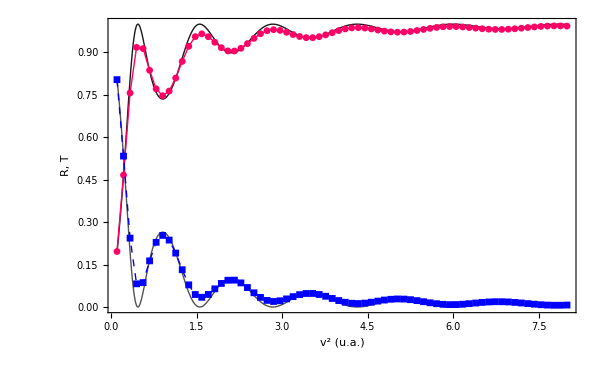

```mathematica
(*================= R(v^2), T(v^2) para una sigma (=Subscript[σ, 0])=================*)

(*---1) Barrido en v^2 (ajustable)---*)
v2Min=0.10;v2Max=8.0;nV2=70;
v2List=Subdivide[v2Min,v2Max,nV2-1];
kList=Sqrt[v2List]*mass/hbar;   (*v=(ħ/m) k*)

(*---2) Hamiltoniano de dispersión:pozo SIN CAP---*)
wellVectorOnly=If[useWell,If[Abs[#-xWell]<=wellWidth/2.,-V0,0.]&/@xInterior,ConstantArray[0.,Length[xInterior]]]//Developer`ToPackedArray;

Htr=N[-(hbar^2/(2. mass))*laplacian+SparseArray[Band[{1,1}]->wellVectorOnly]];

idMatTR=IdentityMatrix[Length[xInterior],SparseArray];
aTR=N[idMatTR+I*(dt/(2. hbar))*Htr];
bTR=N[idMatTR-I*(dt/(2. hbar))*Htr];
solverTR=LinearSolve[aTR];
cnStepTR[psi_]:=solverTR[bTR.psi];

(*---3) Utilidades físicas---*)
probTot[rho_]:=dx*Total[rho];
leftMask=UnitStep[-xInterior];   (*x<=0->reflexión*)
rightMask=UnitStep[xInterior];    (*x>=0->transmisión*)
probLeft[rho_]:=dx*Total[leftMask*rho];
probRight[rho_]:=dx*Total[rightMask*rho];

(*paquete inicial normalizado para un k dado;usa sigma0 del paso 1*)
envTR[x_]:=Exp[-(x-x0)^2/(2. sigma0^2)];
psi0TR[k_?NumericQ]:=Module[{psi=(envTR/@xInterior)*Exp[I*k*xInterior]},Developer`ToPackedArray@N[psi/norm1D[psi]]];

(*tiempo “suficiente” hasta t≈2|x0|/vg*)
stepsForK[k_?NumericQ]:=Module[{vg=(hbar*k)/mass,tMaxK},tMaxK=2.*Abs[x0]/Max[vg,1.*^-12];
Max[0,Floor[tMaxK/dt]]];

(*calcula {v2,T,R} para un k*)
TRforK[k_?NumericQ]:=Module[{psi=psi0TR[k],steps=stepsForK[k],rho,pL,pR,pT,v2},Do[psi=cnStepTR[psi],{steps}];
rho=Developer`ToPackedArray@Abs[psi]^2;
pL=probLeft[rho];pR=probRight[rho];pT=probTot[rho];
v2=(hbar*k/mass)^2;
{v2,pR/pT,pL/pT}           (*{v2,Tnum,Rnum}*)];

(*ejecuta el barrido*)
numData=TRforK/@kList;
tPts=numData[[All,{1,2}]];    (*(v2,Tnum)*)
rPts=numData[[All,{1,3}]];    (*(v2,Rnum)*)

(*---4) Curvas analíticas de Griffiths para pozo finito---*)
aHalf=wellWidth/2.;
EfromV2[v2_]:=(mass/2.)*v2;
TanalyticE[E_]:=1./(1.+(V0^2/(4. E (E+V0)))*Sin[(2. aHalf/hbar)*Sqrt[2. mass (E+V0)]]^2);
TanalyticV2[v2_]:=TanalyticE[EfromV2[v2]];
RanalyticV2[v2_]:=1.-TanalyticV2[v2];

pltAnalytic=Plot[Evaluate@{TanalyticV2[v2],RanalyticV2[v2]},{v2,v2Min,v2Max},PlotRange->{0,1},Exclusions->None,PlotStyle->{Directive[Thick,Black,Opacity[.9]],Directive[Thick,GrayLevel[.25],Opacity[.9]]}];

(*---5) Curvas numéricas (línea+puntos)---*)
tColor=RGBColor[1,0,0.4];   
rColor=RGBColor[0,0,1];     
pltNum={ListLinePlot[tPts,PlotRange->{{v2Min,v2Max},{0,1}},PlotStyle->Directive[tColor,Thin],PlotMarkers->{"●",7}],ListLinePlot[rPts,PlotRange->{{v2Min,v2Max},{0,1}},PlotStyle->Directive[rColor,Thin,Dashed],(*conserva línea discontinua si te gusta*)PlotMarkers->{"■",7}            (*cuadrado lleno*)]};
(*---6) Figura final con leyenda clara (robusta)---*)(*leyenda compuesta:líneas (analítico)+puntos con marcadores (numérico)*)legendObj=Column[{LineLegend[{Directive[Black,Thick],Directive[GrayLevel[.25],Thick]},{"T analítico","R analítico"},LegendLayout->"Column"],PointLegend[{tColor,Directive[rColor,Dashed]},{"T num (σ = "<>ToString@NumberForm[sigma0,{4,1}]<>")","R num (σ = "<>ToString@NumberForm[sigma0,{4,1}]<>")"},LegendMarkers->{{"●",10},{"■",10}},LegendLayout->"Column"]},Spacings->.6];

(*primero juntamos las curvas*)
gRT=Show[Join[{pltAnalytic},pltNum],Frame->True,Axes->False,FrameLabel->(Style[#,20]&/@{"\!\(\*SuperscriptBox[\(v\), \(2\)]\) (u.a.)","R, T"}),PlotRange->{{v2Min,v2Max},{0,1}},ImageSize->600,PlotRangePadding->Scaled[.02]];
(*ahora sí,adjuntamos la leyenda*)
pltRTsingle=Legended[gRT,Placed[legendObj,{0.50,0.50}]];
pltRTsingle
```

#### Escala logaritmica

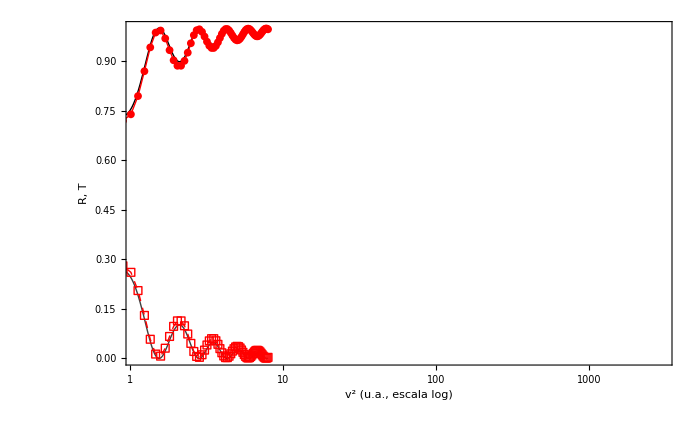

```mathematica
(* ===R(v^2),T(v^2) con eje x logarítmico===*)pltAnalyticLog=Plot[Evaluate@{TanalyticV2[v2],RanalyticV2[v2]},{v2,v2Min,v2Max},PlotRange->{0,1},Exclusions->None,PlotStyle->{Directive[Black,Thin],Directive[GrayLevel[.25],Thin]},ScalingFunctions->{"Log",None}];pltNumLog={ListLinePlot[tPts,PlotRange->{{v2Min,v2Max},{0,1}},PlotStyle->Directive[numColor,Thin],PlotMarkers->{"●",8},ScalingFunctions->{"Log",None}],ListLinePlot[rPts,PlotRange->{{v2Min,v2Max},{0,1}},PlotStyle->Directive[numColor,Thin,Dashed],PlotMarkers->{"□",8},ScalingFunctions->{"Log",None}]};gRTlog=Show[Join[{pltAnalyticLog},pltNumLog],Frame->True,Axes->False,FrameLabel->(Style[#,16]&/@{"\!\(\*SuperscriptBox[\(v\), \(2\)]\) (u.a., escala \ log)","R, T"}),PlotRange->{{v2Min,v2Max},{0,1}},ImageSize->700,PlotRangePadding->Scaled[.02]];pltRTsingleLog=Legended[gRTlog,Placed[legendObj,{0.15,0.45}]];pltRTsingleLog
```

#### Sigmas

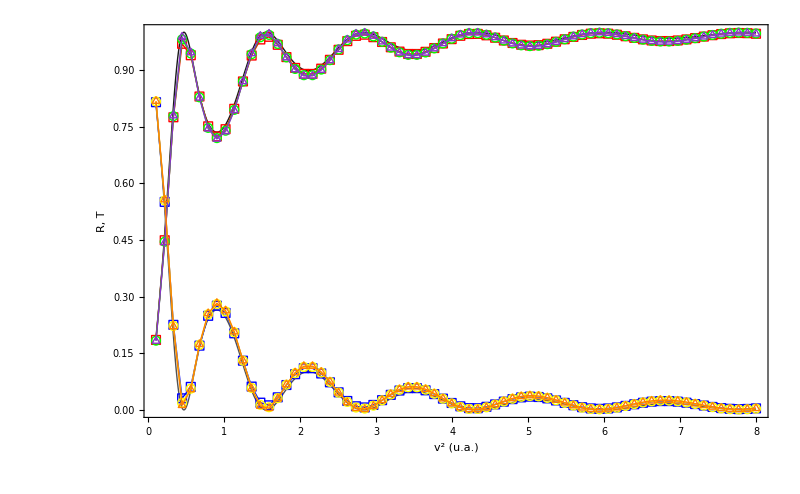

```mathematica
(* =================PASO 3:T,R para TRES sigmas=================*)
sigmaList={20.,30.,50.};   (* <---AJUSTA AQUÍ tus dispersiones*)

(*---1) Paquete inicial para σ arbitraria (igual que psi0TR pero con σ variable)---*)
psi0TRsigma[k_?NumericQ,sigma_?NumericQ]:=Module[{env=Exp[-(xInterior-x0)^2/(2. sigma^2)],psi},psi=env*Exp[I*k*xInterior];
Developer`ToPackedArray@N[psi/Sqrt[dx*Total[Abs[psi]^2]]]];

(*---2) Medición de T y R para un (k,σ) dado reutilizando solverTR/cnStepTR---*)
TRforKsigma[k_?NumericQ,sigma_?NumericQ]:=Module[{psi=psi0TRsigma[k,sigma],steps=stepsForK[k],rho,pL,pR,pT},Do[psi=cnStepTR[psi],{steps}];
rho=Developer`ToPackedArray@Abs[psi]^2;
pL=probLeft[rho];pR=probRight[rho];pT=probTot[rho];
{(hbar*k/mass)^2,pR/pT,pL/pT}   (*{v2,T,R}*)];

(*---3) Corre el barrido para cada σ de sigmaList sobre tu kList ya definido---*)
runForSigma[sigma_?NumericQ]:=Module[{tab=TRforKsigma[#,sigma]&/@kList},<|"sigma"->sigma,"Tpts"->tab[[All,{1,2}]],"Rpts"->tab[[All,{1,3}]]|>];

allData3=runForSigma/@sigmaList;

(*---4) Curvas analíticas (ya tienes TanalyticV2 y RanalyticV2 definidos)---*)
pltAnalytic3=Plot[Evaluate@{TanalyticV2[v2],RanalyticV2[v2]},{v2,v2Min,v2Max},PlotRange->{0,1},Exclusions->None,PlotStyle->{Directive[Thick,Black,Opacity[.9]],Directive[Thick,GrayLevel[.25],Opacity[.9]]}];

(*---Estilos personalizados por σ y por observable (T o R)---*)
mSquare="□";
mCircle="○"; 
mTriangle="△";

(*colores*)
colR20=Blue;colT20=Red;
colR30=Yellow;colT30=Green;
colR50=Orange;colT50=RGBColor[0.55,0.20,0.80];  (*violeta/morado*)

(*funciones que devuelven {color,marcador} por σ y tipo "T" o "R"*)
colorMarkerFor[sigma_,kind_]:=Switch[{N@sigma,kind},{20.,"R"},{colR20,mSquare},{20.,"T"},{colT20,mSquare},{30.,"R"},{colR30,mCircle},{30.,"T"},{colT30,mCircle},{50.,"R"},{colR50,mTriangle},{50.,"T"},{colT50,mTriangle},_,{Gray,mCircle}             (*respaldo por si acaso*)];

(*---Curvas numéricas con Thin y marcador correspondiente---*)
plotsNum3=Flatten@Map[Function[dat,Module[{σ=dat["sigma"],colM,colT,markR,markT},{colM,markR}=colorMarkerFor[σ,"R"];
{colT,markT}=colorMarkerFor[σ,"T"];
{ListLinePlot[dat["Tpts"],PlotRange->{{v2Min,v2Max},{0,1}},PlotStyle->Directive[colT,Thin],PlotMarkers->{markT,9}],ListLinePlot[dat["Rpts"],PlotRange->{{v2Min,v2Max},{0,1}},PlotStyle->Directive[colM,Thin],PlotMarkers->{markR,9}]}]],allData3];

(*---Leyenda:analítico (líneas gruesas)+6 entradas numéricas (línea+marcador)---*)
legendAnalitico=LineLegend[{Directive[Black,Thick],Directive[GrayLevel[.25],Thick]},{"T analítico (negro)","R analítico (gris)"},LegendLayout->"Column"];

numStyles={Directive[colT20,Thin],Directive[colR20,Thin],Directive[colT30,Thin],Directive[colR30,Thin],Directive[colT50,Thin],Directive[colR50,Thin]};

numMarkers={{mSquare,9},{mSquare,9},(*σ=20:cuadrados*){mCircle,9},{mCircle,9},(*σ=30:círculos*){mTriangle,9},{mTriangle,9} (*σ=50:triángulos*)};

numLabels={"T num (σ = 20)","R num (σ = 20)","T num (σ = 30)","R num (σ = 30)","T num (σ = 50)","R num (σ = 50)"};

legendNumerico=LineLegend[numStyles,numLabels,LegendMarkers->numMarkers,LegendLayout->"Column"];

legendObj=Column[{legendAnalitico,legendNumerico},Spacings->.6];

(*---Figura final (las analíticas siguen gruesas y sin cambios)---*)
pltTR3sigmas=Legended[Show[Join[{pltAnalytic3},plotsNum3],Frame->True,Axes->False,FrameLabel->(Style[#,16]&/@{"\!\(\*SuperscriptBox[\(v\), \(2\)]\) (u.a.)","R, T"}),PlotRange->{{v2Min,v2Max},{0,1}},ImageSize->800,PlotRangePadding->Scaled[.02]],Placed[legendObj,{0.50,0.50}]   (*mueve la leyenda si lo deseas*)];

pltTR3sigmas
```

```mathematica
outDir="/home/ej-hdez/Descargas/RyT";

If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];

Export[FileNameJoin[{outDir,"Gauss0-R,T(NyA).pdf"}],pltRTsingle];
Export[FileNameJoin[{outDir,"3sigmas-R,T(NyA).pdf"}],pltTR3sigmas];
```